# Computation of S Parameters in Arbitrary Passive Networks

## Marcel Utz, University of Southampton July 2015 August 2017

Package Implementation and Documentation

## Package initialisation etc

```mathematica
BeginPackage["NodeNetwork`"];

NodeNetwork::VersionNumber="0.0.5";

Print["Linear Nodal Network Analysis
Version ", NodeNetwork::VersionNumber, "
(c)2015-2017 Marcel Utz
marcel.utz@southampton.ac.uk"];
```

Linear Nodal Network Analysis
Version 0.0.5
(c)2015-2017 Marcel Utz
marcel.utz@southampton.ac.uk

### Revision History

#### 0.0.0

Project start.

#### 0.0.1

sufficient functionality for simple calculations.

#### 0.0.2

changed definition of SMatrix[ ], ZMatrix[ ], and PortMatrix[ ] to determine the number of ports automatically from the length of the port list.

#### 0.0.3

added power dissipation analysis (BranchPower[ ], BranchVoltage[ ], and BranchCurrent[ ]);
added dissipation factor to capacitors

#### 0.0.4

added support for transmission lines connecting to pairs of nodes

#### 0.0.5

implemented Branch voltage and Power calculations for four-pole elements

## Nodal Admittance Matrix

### Implementation

```mathematica
AdmittanceMatrix[nnodes_,BL_,OptionsPattern[{FullMatrix->False}]]:= Module[{l,A,Y,k,m,n},
Y=SparseArray[{},{nnodes,nnodes},0];
Do[ 
	If[Length[b]==2,  (* Two-pole admittance *)
		{k,m}= b [[1]];  (* pair of node defining the port *)
		Y[[k,m]] += -b[[2]];  (* b[[2]] is the port admittance of the two-pole *)
		Y[[m,k]] += -b[[2]];
		Y[[k,k]] += b[[2]];
		Y[[m,m]] += b[[2]];
	];
	If[Length[b]==3,  (* Four-pole admittance *)
		{k,l,m,n}= b[[1]]; (* two pairs of input nodes define the ports *)
		Do[Y[[x,x]] += b[[2]],{x,{k,l,m,n}}]; (* b[[2]] is the diagonal and b[[3]] the off-diagonal element of two-port admittance *)
		Y[[k,l]]+=-b[[2]];
		Y[[k,m]]+= b[[3]];
		Y[[k,n]]+= -b[[3]];
		Y[[l,k]]+= -b[[2]];
		Y[[l,m]]+= -b[[3]];
		Y[[l,n]]+= b[[3]];
		Y[[m,k]]+= b[[3]];
		Y[[m,l]]+= -b[[3]];
		Y[[m,n]]+= -b[[2]];
		Y[[n,k]]+= -b[[3]];
		Y[[n,l]]+= -b[[3]];
		Y[[n,m]]+= -b[[2]];
	];		
,{b,BL}] ;
If[OptionValue[FullMatrix]==True, Y, Y[[2;;,2;;]] ]
];
```

### Usage String

AdmittanceMatrix[n, B] computes the nodal admittance matrix of dimensions (n-1) × (n-1) from the list of network branches B. The branch list is an array of elements of the form { {n,m}, Y}, where n and m are the nodes the branch connects, and Y is the branch admittance. By definition, node 1 is assumed to be ground, and all voltages are taken with reference to it. By default, AdmittanceMatrix returns the reduced matrix, without the row and column related to the ground node. This can be changed by setting the option FullMatrix→False.

```mathematica
NotebookRead[PreviousCell[]]  /. Cell[TextData[txt_],___]:> 
		StringJoin[Table[ToString[DisplayForm[t],StandardForm],{t,txt}]]
```

AdmittanceMatrix[n, B] computes the nodal admittance matrix of dimensions (n-1) × (n-1) from the list of network branches B. The branch list is an array of elements of the form { {n,m}, Y}, where n and m are the nodes the branch connects, and Y is the branch admittance. By definition, node 1 is assumed to be ground, and all voltages are taken with reference to it. By default, AdmittanceMatrix returns the reduced matrix, without the row and column related to the ground node. This can be changed by setting the option FullMatrix→False.

```mathematica
AdmittanceMatrix::usage="\!\(\*TagBox[StyleBox[\"AdmittanceMatrix\", Rule[FontFamily, \"Courier\"]], DisplayForm]\)\!\(\*TagBox[\"\\\"[\\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`\(\(\(n,\\ B\)\)]\)\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" computes the nodal admittance matrix of dimensions \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`\(\(\((n - 1)\)\)\\ ×\\ \(\((n - 1)\)\)\)\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" from the list of network branches \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`B\)]], DisplayForm]\)\!\(\*TagBox[\"\\\". The branch list is an array of elements of the form \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`\({\\ \(\({n, m}\)\),\\ Y}\)\)]], DisplayForm]\)\!\(\*TagBox[\"\\\", where \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`n\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" and \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`m\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" are the nodes the branch connects, and \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`Y\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" is the branch admittance. By definition, node 1 is assumed to be ground, and all voltages are taken with reference to it. By default, \\\"\", DisplayForm]\)\!\(\*TagBox[StyleBox[\"AdmittanceMatrix\", Rule[FontFamily, \"Courier\"]], DisplayForm]\)\!\(\*TagBox[\"\\\" returns the reduced matrix, without the row and column related to the ground node. This can be changed by setting the option \\\"\", DisplayForm]\)\!\(\*TagBox[StyleBox[\"FullMatrix→False.\", Rule[FontFamily, \"Courier\"]], DisplayForm]\)"
```

AdmittanceMatrix[TraditionalForm`n, B] computes the nodal admittance matrix of dimensions TraditionalForm`(n - 1) × (n - 1) from the list of network branches TraditionalForm`B. The branch list is an array of elements of the form TraditionalForm`{ {n, m}, Y}, where TraditionalForm`n and TraditionalForm`m are the nodes the branch connects, and TraditionalForm`Y is the branch admittance. By definition, node 1 is assumed to be ground, and all voltages are taken with reference to it. By default, AdmittanceMatrix returns the reduced matrix, without the row and column related to the ground node. This can be changed by setting the option FullMatrix→False.

### Simple Example: Tuned/matched resonator

```mathematica
?AdmittanceMatrix
```

TagBox[StyleBox["AdmittanceMatrix", Rule[FontFamily, "Courier"]], DisplayForm]TagBox["\"[\"", DisplayForm]TraditionalForm`n,\ B]TagBox["\" computes the nodal admittance matrix of dimensions \"", DisplayForm]TraditionalForm`(n - 1)\ ×\ (n - 1)TagBox["\" from the list of network branches \"", DisplayForm]TraditionalForm`BTagBox["\". The branch list is an array of elements of the form \"", DisplayForm]TraditionalForm`{\ {n, m},\ Y}TagBox["\", where \"", DisplayForm]TraditionalForm`nTagBox["\" and \"", DisplayForm]TraditionalForm`mTagBox["\" are the nodes the branch connects, and \"", DisplayForm]TraditionalForm`YTagBox["\" is the branch admittance. By definition, node 1 is assumed to be ground, and all voltages are taken with reference to it. By default, \"", DisplayForm]TagBox[StyleBox["AdmittanceMatrix", Rule[FontFamily, "Courier"]], DisplayForm]TagBox["\" returns the reduced matrix, without the row and column related to the ground node. This can be changed by setting the option \"", DisplayForm]TagBox[StyleBox["FullMatrix→False.", Rule[FontFamily, "Courier"]], DisplayForm]

In the following, we will demonstrate the use of the package by some simple examples. The first one is a resonator consisting of a parallel RLC circuit, connected to a transmission line using a matching capacitor.

```mathematica
BranchList={{{2,3},I ω CM}, {{3,1},I ω CT},{{3,1},1/(I ω LT +R)}}
```

{{{2,3},ⅈ CM ω},{{3,1},ⅈ CT ω},{{3,1},1/(R+ⅈ LT ω)}}

```mathematica
(Y=AdmittanceMatrix[3,BranchList]) // MatrixForm
```

(ⅈ CM ω | -ⅈ CM ω
-ⅈ CM ω | ⅈ CM ω+ⅈ CT ω+1/(R+ⅈ LT ω))

```mathematica
MatrixRank[Y]
```

2

```mathematica
(Y=AdmittanceMatrix[3,BranchList,FullMatrix->True]) // MatrixForm
```

(ⅈ CT ω+1/(R+ⅈ LT ω) | 0 | -ⅈ CT ω-1/(R+ⅈ LT ω)
0 | ⅈ CM ω | -ⅈ CM ω
-ⅈ CT ω-1/(R+ⅈ LT ω) | -ⅈ CM ω | ⅈ CM ω+ⅈ CT ω+1/(R+ⅈ LT ω))

```mathematica
MatrixRank[Y]
```

2

### Another Example: Open-ended Transmission Line

```mathematica
BranchList = {{{2,1,3,4},Coth[γ l]/Z0, Csch[γ l]/Z0}}
```

{{{2,1,3,4},Coth[l γ]/Z0,Csch[l γ]/Z0}}

```mathematica
(Y=AdmittanceMatrix[4,BranchList]) // MatrixForm
```

(Coth[l γ]/Z0 | Csch[l γ]/Z0 | -Csch[l γ]/Z0
Csch[l γ]/Z0 | Coth[l γ]/Z0 | -Coth[l γ]/Z0
-Csch[l γ]/Z0 | -Coth[l γ]/Z0 | Coth[l γ]/Z0)

## Port Matrix

### Implementation

```mathematica
PortMatrix[nnodes_,PL_,OptionsPattern[{FullMatrix->False}]]:= Module[{nports,A,P,k,m},
nports=Length[PL];
P=SparseArray[{},{nnodes,nports},0];
Do[
    {k,m}= PL[[b]];
	P[[k,b]]=1;
	P[[m,b]]=-1;
,{b,1,nports}] ;
If[OptionValue[FullMatrix]==True, P, P[[2;;]] ]
];
```

### Usage string

PortMatrix[n,P] computes the port adjancency matrix of dimensions (n-1) × p from the list of ports P, assuming the network has n nodes and p ports. The list of ports is an array of p elements of the form { {n,m}}, where n and m are the nodes the port connects. By default, PortMatrix returns the reduced matrix, without the row corresponding to the ground node. This can be changed by setting the option FullMatrix→False.

```mathematica
NotebookRead[PreviousCell[]]  /. Cell[TextData[txt_],___]:> 
		StringJoin[Table[ToString[DisplayForm[t],StandardForm],{t,txt}]]
```

PortMatrix[n,P] computes the port adjancency matrix of dimensions (n-1) × p from the list of ports P, assuming the network has n nodes and p ports. The list of ports is an array of p elements of the form { {n,m}}, where n and m are the nodes the port connects. By default, PortMatrix returns the reduced matrix, without the row corresponding to the ground node. This can be changed by setting the option FullMatrix→False.

```mathematica
PortMatrix::usage="\!\(\*TagBox[StyleBox[\"PortMatrix\", Rule[FontFamily, \"Courier\"]], DisplayForm]\)\!\(\*TagBox[\"\\\"[\\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`\(\(\(n, P\)\)]\)\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" computes the port adjancency matrix of dimensions \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`\(\(\((n - 1)\)\)\\ ×\\ p\)\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" from the list of ports \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`P\)]], DisplayForm]\)\!\(\*TagBox[\"\\\", assuming the network has \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`n\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" nodes and \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`p\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" ports. The list of ports is an array of \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`p\)], Rule[FormatType, \"TraditionalForm\"]], DisplayForm]\)\!\(\*TagBox[\"\\\" elements of the form \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`\({\\ \({n, m}\)}\)\)]], DisplayForm]\)\!\(\*TagBox[\"\\\", where \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`n\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" and \\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`m\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" are the nodes the port connects. By default, \\\"\", DisplayForm]\)\!\(\*TagBox[StyleBox[\"PortMatrix\", Rule[FontFamily, \"Courier\"]], DisplayForm]\)\!\(\*TagBox[\"\\\" returns the reduced matrix, without the row corresponding to the ground node. This can be changed by setting the option \\\"\", DisplayForm]\)\!\(\*TagBox[StyleBox[\"FullMatrix→False.\", Rule[FontFamily, \"Courier\"]], DisplayForm]\)"
```

PortMatrix[TraditionalForm`n, P] computes the port adjancency matrix of dimensions TraditionalForm`(n - 1) × p from the list of ports TraditionalForm`P, assuming the network has TraditionalForm`n nodes and TraditionalForm`p ports. The list of ports is an array of TraditionalForm`p elements of the form TraditionalForm`{ {n, m}}, where TraditionalForm`n and TraditionalForm`m are the nodes the port connects. By default, PortMatrix returns the reduced matrix, without the row corresponding to the ground node. This can be changed by setting the option FullMatrix→False.

### Example

```mathematica
?PortMatrix
```

TagBox[StyleBox["PortMatrix", Rule[FontFamily, "Courier"]], DisplayForm]TagBox["\"[\"", DisplayForm]TraditionalForm`n, P]TagBox["\" computes the port adjancency matrix of dimensions \"", DisplayForm]TraditionalForm`(n - 1)\ ×\ pTagBox["\" from the list of ports \"", DisplayForm]TraditionalForm`PTagBox["\", assuming the network has \"", DisplayForm]TraditionalForm`nTagBox["\" nodes and \"", DisplayForm]TraditionalForm`pTagBox["\" ports. The list of ports is an array of \"", DisplayForm]TagBox[Cell[BoxData[TraditionalForm`p], Rule[FormatType, "TraditionalForm"]], DisplayForm]TagBox["\" elements of the form \"", DisplayForm]TraditionalForm`{\ {n, m}}TagBox["\", where \"", DisplayForm]TraditionalForm`nTagBox["\" and \"", DisplayForm]TraditionalForm`mTagBox["\" are the nodes the port connects. By default, \"", DisplayForm]TagBox[StyleBox["PortMatrix", Rule[FontFamily, "Courier"]], DisplayForm]TagBox["\" returns the reduced matrix, without the row corresponding to the ground node. This can be changed by setting the option \"", DisplayForm]TagBox[StyleBox["FullMatrix→False.", Rule[FontFamily, "Courier"]], DisplayForm]

TagBox[
StyleBox["PortMatrix",
FontFamily->"Courier"],
DisplayForm]TagBox["\"<[>\"",
DisplayForm]TagBox[Cell[BoxData[
FormBox[
RowBox[{
RowBox[{"n", ",", "P"}], "]"}], TraditionalForm]]],
DisplayForm]TagBox["\"< computes the port adjancency matrix of dimensions >\"",
DisplayForm]TagBox[Cell[BoxData[
FormBox[
RowBox[{
RowBox[{"(", 
RowBox[{"n", "-", "1"}], ")"}], " ", "×", " ", "p"}], TraditionalForm]]],
DisplayForm]TagBox["\"< from the list of ports >\"",
DisplayForm]TagBox[Cell[BoxData[
FormBox["P", TraditionalForm]]],
DisplayForm]TagBox["\"<, assuming the network has >\"",
DisplayForm]TagBox[Cell[BoxData[
FormBox["n", TraditionalForm]]],
DisplayForm]TagBox["\"< nodes and >\"",
DisplayForm]TagBox[Cell[BoxData[
FormBox["p", TraditionalForm]]],
DisplayForm]TagBox["\"< ports. The list of ports is an array of >\"",
DisplayForm]TagBox[Cell[BoxData[
FormBox["p", TraditionalForm]]],
DisplayForm]TagBox["\"< elements of the form >\"",
DisplayForm]TagBox[Cell[BoxData[
FormBox[
RowBox[{"{", " ", 
RowBox[{"{", 
RowBox[{"n", ",", "m"}], "}"}], "}"}], TraditionalForm]]],
DisplayForm]TagBox["\"<, where >\"",
DisplayForm]TagBox[Cell[BoxData[
FormBox["n", TraditionalForm]]],
DisplayForm]TagBox["\"< and >\"",
DisplayForm]TagBox[Cell[BoxData[
FormBox["m", TraditionalForm]]],
DisplayForm]TagBox["\"< are the nodes the port connects. By default, >\"",
DisplayForm]TagBox[
StyleBox["PortMatrix",
FontFamily->"Courier"],
DisplayForm]TagBox["\"< returns the reduced matrix, without the row corresponding to the ground node. This can be changed by setting the option >\"",
DisplayForm]TagBox[
StyleBox[
RowBox[{"FullMatrix", "→", 
RowBox[{"False", "."}]}],
FontFamily->"Courier"],
DisplayForm]

```mathematica
PortList = {{2,1}}
```

{{2,1}}

```mathematica
P=PortMatrix[3,PortList,FullMatrix->True]
```

SparseArray[<2>, {3, 1}]

```mathematica
MatrixForm[P]
```

(-1
1
0)

With the branch list and port list, we can now compute the port impedance matrix:

```mathematica
PortList //TableForm
```

2 | 1

```mathematica
BranchList={{{2,3},I ω CM}, {{3,1},I ω CT},{{3,1},1/(I ω LT +R)}}
```

{{{2,3},ⅈ CM ω},{{3,1},ⅈ CT ω},{{3,1},1/(R+ⅈ LT ω)}}

```mathematica
BranchList //TableForm
```

2
3 | ⅈ CM ω
3
1 | ⅈ CT ω
3
1 | 1/(R+ⅈ LT ω)

```mathematica
P=PortMatrix[3,PortList]; 
Y=AdmittanceMatrix[3,BranchList];

ZP = -Transpose[P].LinearSolve[Y,P]
```

{{(ⅈ (-1-ⅈ CM R ω-ⅈ CT R ω+CM LT ω^2+CT LT ω^2))/(CM ω (-1-ⅈ CT R ω+CT LT ω^2))}}

```mathematica
ZP[[1,1]]== (-Transpose[P].Inverse[Y].P)[[1,1]]
```

(ⅈ (-1-ⅈ CM R ω-ⅈ CT R ω+CM LT ω^2+CT LT ω^2))/(CM ω (-1-ⅈ CT R ω+CT LT ω^2))==-(ⅈ CM ω+ⅈ CT ω+1/(R+ⅈ LT ω))/(-CM CT ω^2+(ⅈ CM ω)/(R+ⅈ LT ω))

```mathematica
FullSimplify[%]
```

True

From this, the S parameter matrix (which is 1×1 in this case) can be found by

```mathematica
Sres=LinearSolve[ ZP-Z0 IdentityMatrix[1],ZP + Z0 IdentityMatrix[1]]
```

{{(-1-ⅈ CM R ω-ⅈ CT R ω+ⅈ CM Z0 ω+CM LT ω^2+CT LT ω^2-CM CT R Z0 ω^2-ⅈ CM CT LT Z0 ω^3)/(-1-ⅈ CM R ω-ⅈ CT R ω-ⅈ CM Z0 ω+CM LT ω^2+CT LT ω^2+CM CT R Z0 ω^2+ⅈ CM CT LT Z0 ω^3)}}

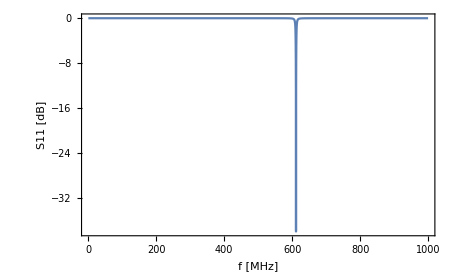

```mathematica
Plot[ 20 Log10[Abs[Sres[[1,1]]]] //. {CT-> 5.4 10^(-6),CM->0.25 10^(-6),LT-> 0.012,Z0->50,R->0.1,ω->2π ν},{ν,0,1000},PlotRange->All,Frame->True,FrameLabel->{"f [MHz]", "S11 [dB]"}]
```

### Another example: open-ended transmission line

```mathematica
BranchListTL = {{{2,1,3,4},Coth[γ l]/Z0, Csch[γ l]/Z0},
		{{3,4},1/Z1}}
```

{{{2,1,3,4},Coth[l γ]/Z0,Csch[l γ]/Z0},{{3,4},1/Z1}}

```mathematica
(Y=AdmittanceMatrix[4,BranchListTL]) // MatrixForm
```

(Coth[l γ]/Z0 | Csch[l γ]/Z0 | -Csch[l γ]/Z0
Csch[l γ]/Z0 | 1/Z1+Coth[l γ]/Z0 | -1/Z1-Coth[l γ]/Z0
-Csch[l γ]/Z0 | -1/Z1-Coth[l γ]/Z0 | 1/Z1+Coth[l γ]/Z0)

```mathematica
PortListTL = {{2,1}}
```

{{2,1}}

```mathematica
P=PortMatrix[4,PortListTL,FullMatrix->True]
```

SparseArray[<2>, {4, 1}]

```mathematica
P=PortMatrix[4,PortListTL]; 
Y=AdmittanceMatrix[4,BranchListTL];

ZP = -Transpose[P].LinearSolve[Y,P]
```

{{-(Z0 (Z0 Coth[l γ]+Z1 Coth[l γ]^2) Tanh[l γ])/(Z0 Coth[l γ]+Z1 Coth[l γ]^2-Z1 Csch[l γ]^2)}}

```mathematica
FullSimplify[%]
```

{{-(Z0 (Z0+Z1 Coth[l γ]))/(Z1+Z0 Coth[l γ])}}

```mathematica
S=LinearSolve[ ZP-Z0 IdentityMatrix[1],ZP + Z0 IdentityMatrix[1]]
```

{{(Z0-Z0 Coth[l γ]+Z1 Coth[l γ]-Z1 Coth[l γ]^2+Z1 Csch[l γ]^2)/(Z0+Z0 Coth[l γ]+Z1 Coth[l γ]+Z1 Coth[l γ]^2-Z1 Csch[l γ]^2)}}

```mathematica
FullSimplify[%]
```

{{(ⅇ^(-2 l γ) (-Z0+Z1))/(Z0+Z1)}}

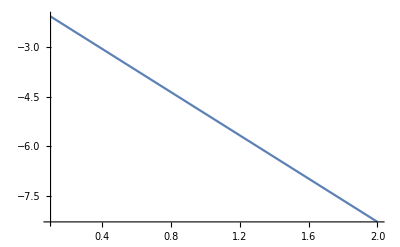

```mathematica
Plot[20Log10[Abs[S[[1,1]]]]/.{γ->2π(I+0.03),Z1->Z0/10},{l,0.1,2}]
```

## Smith Chart Grid

### Implementation

```mathematica
(* Parametrize the resistive r=R/Zo contours *)
SmithR[r_, t_] := { (Cos[t] + r)/(1 + r), Sin[t]/(1 + r) } ;

(* Parametrize the reactive x=X/Zo contours *)
SmithX[x_, t_] := { Cos[t]/x +1, (Sin[t] + 1)/x } ;
```

```mathematica
Solve[SmithX[X,t].SmithX[X,t] == 1,t]
```

{{t→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[ArcTan[-(2 X)/(1+X^2),(-1+X^2)/(1+X^2)]+2 π C[1],C[1]∈Integers]}}

```mathematica
SmithGrid[] := Module[ {SG={}},
SG= Table[ParametricPlot[Evaluate[SmithR[R,t]],{t,0,2Pi},DisplayFunction->Identity,PlotStyle->{Gray,Thickness[0.001]}],{R,0,1,0.2}] ;
SG=Join[SG,Table[ParametricPlot[Evaluate[SmithR[R,t]],{t,0,2Pi},DisplayFunction->Identity,PlotStyle->{Gray,Thickness[0.001]}],{R,1.5,2.5,0.5}]];
SG=Join[SG,Table[ParametricPlot[Evaluate[SmithR[R,t]],{t,0,2Pi},DisplayFunction->Identity,PlotStyle->{Gray,Thickness[0.001]}],{R,4,10,1}]];
SG=Join[SG,Table[ParametricPlot[Evaluate[SmithX[X+0.0001,t]],{t,-π/2 ,ArcTan[-(-1+X^2)/(2X)]},DisplayFunction->Identity,PlotStyle->{Gray,Thickness[0.001]}],{X,-5.0001,0,0.25}]];

SG=Join[SG,Table[ParametricPlot[Evaluate[SmithX[X+0.0001,t]],{t,-π/2,ArcTan[-(2 X)/(1+X^2),(-1+X^2)/(1+X^2)]},DisplayFunction->Identity,PlotStyle->{Gray,Thickness[0.001]}],{X,0.0001,1,0.25}]];

SG=Join[SG,Table[ParametricPlot[Evaluate[SmithX[X+0.0001,t]],{t,3π/2,ArcTan[-(2 X)/(1+X^2),(-1+X^2)/(1+X^2)]},DisplayFunction->Identity,PlotStyle->{Gray,Thickness[0.001]}],{X,1.0001,5,0.25}]];

SG
]
```

### Usage string

SmithGrid[ ] generates a Smith chart grid pattern, which can be used together with polar plots of complex scattering parameters. Usually, the graph and the grid are combined by using:
Show[ParametricPlot[S[ω],{ω,0,2π}], SmithGrid[]]

```mathematica
NotebookRead[PreviousCell[]]  /. Cell[TextData[txt_],___]:> 
		StringJoin[Table[ToString[DisplayForm[t],StandardForm],{t,txt}]]
```

SmithGrid[ ] generates a Smith chart grid pattern, which can be used together with polar plots of complex scattering parameters. Usually, the graph and the grid are combined by using:
Show[ParametricPlot[S[ω],{ω,0,2π}], SmithGrid[]]

```mathematica
SmithGrid::usage="\!\(\*TagBox[StyleBox[\"SmithGrid\", Rule[FontFamily, \"Courier\"]], DisplayForm]\)\!\(\*TagBox[\"\\\"[\\\"\", DisplayForm]\)\!\(\*TagBox[Cell[BoxData[\(TraditionalForm\`\(\\ ]\)\)]], DisplayForm]\)\!\(\*TagBox[\"\\\" generates a Smith chart grid pattern, which can be used together with polar plots of complex scattering parameters. Usually, the graph and the grid are combined by using:\\\\n\\\"\", DisplayForm]\)\!\(\*TagBox[StyleBox[\"Show[ParametricPlot[S[ω],{ω,0,2π}], SmithGrid[]]\", Rule[FontFamily, \"Courier\"]], DisplayForm]\)"
```

SmithGrid[TraditionalForm` ] generates a Smith chart grid pattern, which can be used together with polar plots of complex scattering parameters. Usually, the graph and the grid are combined by using:
Show[ParametricPlot[S[ω],{ω,0,2π}], SmithGrid[]]

### Example

```mathematica
?SmithGrid
```

TagBox[StyleBox["SmithGrid", Rule[FontFamily, "Courier"]], DisplayForm]TagBox["\"[\"", DisplayForm]TraditionalForm`\ ]TagBox["\" generates a Smith chart grid pattern, which can be used together with polar plots of complex scattering parameters. Usually, the graph and the grid are combined by using:\\n\"", DisplayForm]TagBox[StyleBox["Show[ParametricPlot[S[ω],{ω,0,2π}], SmithGrid[]]", Rule[FontFamily, "Courier"]], DisplayForm]

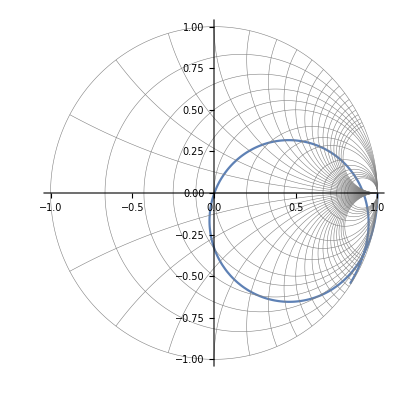

```mathematica
Show[ParametricPlot[{Re[#],Im[#]}& @ Sres[[1,1]] /. {CT-> 0.35 10^(-5),CM->1.65 10^(-6),LT-> 0.02,Z0->50,R->5,ω->2π ν},
{ν,0,1000},PlotRange->{{-1,1},{-1,1}}],SmithGrid[] ]
```

```mathematica
S //. Z1->Z0 // FullSimplify
```

{{0}}

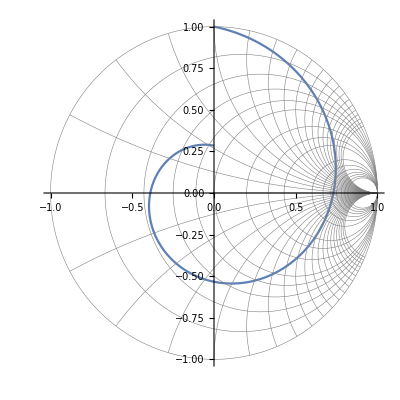

```mathematica
Show[ParametricPlot[{Re[#],Im[#]}& @ S[[1,1]] /. {γ->2π (I+0.2),Z1-> I Z0},
{l,0,1/2},PlotRange->{{-1,1},{-1,1}}],SmithGrid[] ]
```

## Automated S Matrix Computation

### Implementation

```mathematica
ZMatrix[nnodes_, BL_,PL_] := Module[{Y,P},
	P=PortMatrix[nnodes,PL];
	Y=AdmittanceMatrix[nnodes,BL];
	-Transpose[P].LinearSolve[Y,P]
];
```

```mathematica
SMatrix[nnodes_,Z0_,BL_,PL_] := Module[{Z,nports},
	nports=Length[PL];
	Z=ZMatrix[nnodes,BL,PL];
	LinearSolve[ Z-Z0 IdentityMatrix[nports],Z + Z0 IdentityMatrix[nports]]
];
```

### Usage string

ZMatrix[n,B,P] computes the port impedance matrix of dimensions p × p from the list of branches B and the list of ports P, assuming the network has n nodes.

```mathematica
NotebookRead[PreviousCell[]]  /. Cell[TextData[txt_],___]:> 
		StringJoin[Table[ToString[DisplayForm[t],StandardForm],{t,txt}]]
```

ZMatrix[n,B,P] computes the port impedance matrix of dimensions p × p from the list of branches B and the list of ports P, assuming the network has n nodes.

```mathematica
ZMatrix::usage="TagBox[
StyleBox[\"ZMatrix\",
FontFamily->\"Courier\"],
DisplayForm]TagBox[\"\\\"[\\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{ RowBox[{\"n\", \",\", \"B\", \",\", \"P\"}], \"]\"}], TraditionalForm]]], DisplayForm]TagBox[\"\\\" computes the port impedance matrix of dimensions \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{\"p\", \" \", \"×\", \" \", \"p\"}], TraditionalForm]]], DisplayForm]TagBox[\"\\\" from the list of branches \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"B\", TraditionalForm]]], DisplayForm]TagBox[\"\\\" and the list of ports \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"P\", TraditionalForm]]], DisplayForm]TagBox[\"\\\", assuming the network has \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"n\", TraditionalForm]]], DisplayForm]TagBox[\"\\\" nodes.\\\"\", DisplayForm]"
```

ZMatrix[n,B,P] computes the port impedance matrix of dimensions p × p from the list of branches B and the list of ports P, assuming the network has n nodes.

SMatrix[n,Z_0,B,P] computes the port scattering matrix (of dimension p × p) from the list of branches B and the list of ports P, assuming the network has n nodes and p ports with port impedance Z_0.

```mathematica
NotebookRead[PreviousCell[]]  /. Cell[TextData[txt_],___]:> 
		StringJoin[Table[ToString[DisplayForm[t],StandardForm],{t,txt}]]
```

SMatrix[n,Z_0,B,P] computes the port scattering matrix (of dimension p × p) from the list of branches B and the list of ports P, assuming the network has n nodes and p ports with port impedance Z_0.

```mathematica
SMatrix::usage="TagBox[
StyleBox[\"SMatrix\",
FontFamily->\"Courier\"],
DisplayForm]TagBox[\"\\\"[\\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{ RowBox[{\"n\", \",\",  SubscriptBox[\"Z\", \"0\"], \",\", \"B\", \",\", \"P\"}], \"]\"}], TraditionalForm]]], DisplayForm]TagBox[\"\\\" computes the port scattering matrix (of dimension \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{\"p\", \" \", \"×\", \" \", \"p\"}], TraditionalForm]]], DisplayForm]TagBox[\"\\\") from the list of branches \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"B\", TraditionalForm]]], DisplayForm]TagBox[\"\\\" and the list of ports \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"P\", TraditionalForm]]], DisplayForm]TagBox[\"\\\", assuming the network has \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"n\", TraditionalForm]]], DisplayForm]TagBox[\"\\\" nodes and \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"p\", TraditionalForm]]], DisplayForm]TagBox[\"\\\" ports with port impedance \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[ SubscriptBox[\"Z\", \"0\"], TraditionalForm]]], DisplayForm]TagBox[\"\\\".\\\"\", DisplayForm]"
```

SMatrix[n,Z_0,B,P] computes the port scattering matrix (of dimension p × p) from the list of branches B and the list of ports P, assuming the network has n nodes and p ports with port impedance Z_0.

### Examples

```mathematica
?ZMatrix
```

TagBox[
StyleBox["ZMatrix",
FontFamily->"Courier"],
DisplayForm]TagBox["\"[\"", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{ RowBox[{"n", ",", "B", ",", "P"}], "]"}], TraditionalForm]]], DisplayForm]TagBox["\" computes the port impedance matrix of dimensions \"", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{"p", " ", "×", " ", "p"}], TraditionalForm]]], DisplayForm]TagBox["\" from the list of branches \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["B", TraditionalForm]]], DisplayForm]TagBox["\" and the list of ports \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["P", TraditionalForm]]], DisplayForm]TagBox["\", assuming the network has \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["n", TraditionalForm]]], DisplayForm]TagBox["\" nodes.\"", DisplayForm]

```mathematica
?SMatrix
```

TagBox[
StyleBox["SMatrix",
FontFamily->"Courier"],
DisplayForm]TagBox["\"[\"", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{ RowBox[{"n", ",",  SubscriptBox["Z", "0"], ",", "B", ",", "P"}], "]"}], TraditionalForm]]], DisplayForm]TagBox["\" computes the port scattering matrix (of dimension \"", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{"p", " ", "×", " ", "p"}], TraditionalForm]]], DisplayForm]TagBox["\") from the list of branches \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["B", TraditionalForm]]], DisplayForm]TagBox["\" and the list of ports \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["P", TraditionalForm]]], DisplayForm]TagBox["\", assuming the network has \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["n", TraditionalForm]]], DisplayForm]TagBox["\" nodes and \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["p", TraditionalForm]]], DisplayForm]TagBox["\" ports with port impedance \"", DisplayForm]TagBox[Cell[BoxData[ FormBox[ SubscriptBox["Z", "0"], TraditionalForm]]], DisplayForm]TagBox["\".\"", DisplayForm]

```mathematica
S=SMatrix[3,Z0,BranchList,PortList]
```

{{(-1-ⅈ CM R ω-ⅈ CT R ω+ⅈ CM Z0 ω+CM LT ω^2+CT LT ω^2-CM CT R Z0 ω^2-ⅈ CM CT LT Z0 ω^3)/(-1-ⅈ CM R ω-ⅈ CT R ω-ⅈ CM Z0 ω+CM LT ω^2+CT LT ω^2+CM CT R Z0 ω^2+ⅈ CM CT LT Z0 ω^3)}}

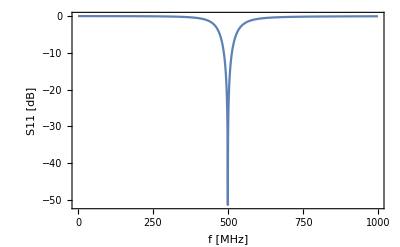

```mathematica
Plot[ 20 Log10[Abs[S[[1,1]]]] //. {CT-> 0.35 10^(-5),CM->1.65 10^(-6),LT-> 0.02,Z0->50,R->5,ω->2π ν},{ν,0,1000},PlotRange->All,Frame->True,FrameLabel->{"f [MHz]", "S11 [dB]"}]
```

## Components and Networks

```mathematica
LumpedComponentRules = {
	Resistor[R_]-> 1/R,
	Capacitor[C1_,DF_:0]->( ω C1 / (DF-I) ),
	Inductor[L_,R_:0]->1/(R+I ω L)} ;

TransmissionLineRules = {
	ShortedTL[ω0_,Z0_,R_:0] -> 1/(R+I Z0 Tan[π/2  ω/ω0]),
	OpenTL[ω0_,Z0_,R_:0] -> 1/(R+I Z0 Cot[π/2  ω/ω0]),
	TransmissionLine[ω0_,Z0_,Z1_] -> (1/Z0 (Z0 Cos[π/2 ω/ω0] + I Z1 Sin[π/2 ω/ω0])/(I Z0 Sin[π/2 ω/ω0] + Z1 Cos[π/2 ω/ω0]))
} ;

ComponentRules = Join[LumpedComponentRules,TransmissionLineRules];
```

```mathematica
TransmissionLine[ω0,Z0,R] /. ComponentRules
```

(Z0 Cos[(π ω)/(2 ω0)]+ⅈ R Sin[(π ω)/(2 ω0)])/(Z0 (R Cos[(π ω)/(2 ω0)]+ⅈ Z0 Sin[(π ω)/(2 ω0)]))

```mathematica
Limit[%,R->Infinity]
```

(ⅈ Tan[(π ω)/(2 ω0)])/Z0

```mathematica
Limit[%%,R->0]
```

-(ⅈ Cot[(π ω)/(2 ω0)])/Z0

```mathematica
OpenTL[ω0,Z0] /. ComponentRules
```

-(ⅈ Tan[(π ω)/(2 ω0)])/Z0

```mathematica
ShortedTL[ω0,Z0] /. ComponentRules
```

-(ⅈ Cot[(π ω)/(2 ω0)])/Z0

## Branch voltages, -currents, and -power

### Implementation

```mathematica
BranchVoltage[nnodes_, BL_,PL_,Ip_] := Module[{Y,P,Vn,k,l,n,m},
	P=PortMatrix[nnodes,PL];
	Y=AdmittanceMatrix[nnodes,BL];
	Vn=-LinearSolve[Y,P].Ip;          (* These are the node voltages *)
	Vn = Prepend[Vn, 0 Ip[[1]] ];     (* Add the ground node to the list, Voltage is 0 by definition *)
	Table[
		If[Length[b]==2,
			{k,l}=b[[1]] ;
			Vn[[k]]-Vn[[l]],
		If[Length[b]==3,
			{k,l,m,n}=b[[1]] ;
			{Vn[[k]]-Vn[[l]],Vn[[m]]-Vn[[n]]}
			]],
	{b,BL}
	]
];
```

```mathematica
BranchCurrent[nnodes_, BL_,PL_,Ip_] := Module[{Vb},
	Vb=BranchVoltage[nnodes,BL,PL,Ip];
	Cases[BL,A_/;Length[A]==2][[;;,2]] Vb
];
```

```mathematica
BranchPower[nnodes_, BL_,PL_,Ip_] := Module[{Vb,P=0,j},
	Vb=BranchVoltage[nnodes,BL,PL,Ip];
	Table[
	  If[Length[BL[[j]] ]==2,
	     1/2 BL[[j,2]] Vb[[j]] Conjugate[Vb[[j]]],
	     If[Length[BL[[j]]]==3,
	        1/2 Conjugate[Vb[[j]]] . {{BL[[j,2]],BL[[j,3]]},{BL[[j,3]],BL[[j,2]]}} . Vb[[j]]]],
	{j,1,Length[BL]}]
];
```

### Usage string

BranchVoltage[ n, B, P, I], BranchCurrent[ n, B, P, I], and BranchPower[ n, B, P, I] return a vector of voltage differences, currents, or average power disspation accross each branch in the branch list B, assuming a network of n nodes, and currents I in the ports. BranchPower[ ] returns a complex value, with the real and imaginary parts representing the dissipated and stored power, respectively.

```mathematica
NotebookRead[PreviousCell[]]  /. Cell[TextData[txt_],___]:> 
		StringJoin[Table[ToString[DisplayForm[t],StandardForm],{t,txt}]]
```

BranchVoltage[ n, B, P, I], BranchCurrent[ n, B, P, I], and BranchPower[ n, B, P, I] return a vector of voltage differences, currents, or average power disspation accross each branch in the branch list B, assuming a network of n nodes, and currents I in the ports. BranchPower[ ] returns a complex value, with the real and imaginary parts representing the dissipated and stored power, respectively.

```mathematica
BranchVoltage::usage="TagBox[
StyleBox[\"BranchVoltage\",
FontFamily->\"Courier\"],
DisplayForm]TagBox[\"\\\"[\\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{\" \",  RowBox[{\"n\", \",\", \" \", \"B\", \",\", \" \", \"P\", \",\", \" \", \"I\"}], \"]\"}], TraditionalForm]]], DisplayForm]TagBox[\"\\\", \\\"\", DisplayForm]TagBox[ StyleBox[\"BranchCurrent\", FontFamily->\"Courier\"], DisplayForm]TagBox[\"\\\"[\\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{\" \",  RowBox[{\"n\", \",\", \" \", \"B\", \",\", \" \", \"P\", \",\", \" \", \"I\"}], \"]\"}], TraditionalForm]]], DisplayForm]TagBox[\"\\\", and \\\"\", DisplayForm]TagBox[ StyleBox[\"BranchPower\", FontFamily->\"Courier\"], DisplayForm]TagBox[\"\\\"[\\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{\" \",  RowBox[{\"n\", \",\", \" \", \"B\", \",\", \" \", \"P\", \",\", \" \", \"I\"}], \"]\"}], TraditionalForm]]], DisplayForm]TagBox[\"\\\" return a vector of voltage differences, currents, or average power disspation accross each branch in the branch list \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"B\", TraditionalForm]]], DisplayForm]TagBox[\"\\\", assuming a network of \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"n\", TraditionalForm]]], DisplayForm]TagBox[\"\\\" nodes, and currents \\\"\", DisplayForm]TagBox[Cell[BoxData[ FormBox[\"I\", TraditionalForm]]], DisplayForm]TagBox[\"\\\" in the ports. \\\"\", DisplayForm]TagBox[ StyleBox[\"BranchPower\", FontFamily->\"Courier\"], DisplayForm]TagBox[\"\\\"[ ] returns a complex value, with the real and imaginary parts representing the dissipated and stored power, respectively.\\\"\", DisplayForm]"
```

BranchVoltage[ n, B, P, I], BranchCurrent[ n, B, P, I], and BranchPower[ n, B, P, I] return a vector of voltage differences, currents, or average power disspation accross each branch in the branch list B, assuming a network of n nodes, and currents I in the ports. BranchPower[ ] returns a complex value, with the real and imaginary parts representing the dissipated and stored power, respectively.

```mathematica
BranchCurrent::usage=BranchVoltage::usage; BranchPower::usage=BranchVoltage::usage;
```

### Example

```mathematica
?BranchPower
```

TagBox[
StyleBox["BranchVoltage",
FontFamily->"Courier"],
DisplayForm]TagBox["\"[\"", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{" ",  RowBox[{"n", ",", " ", "B", ",", " ", "P", ",", " ", "I"}], "]"}], TraditionalForm]]], DisplayForm]TagBox["\", \"", DisplayForm]TagBox[ StyleBox["BranchCurrent", FontFamily->"Courier"], DisplayForm]TagBox["\"[\"", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{" ",  RowBox[{"n", ",", " ", "B", ",", " ", "P", ",", " ", "I"}], "]"}], TraditionalForm]]], DisplayForm]TagBox["\", and \"", DisplayForm]TagBox[ StyleBox["BranchPower", FontFamily->"Courier"], DisplayForm]TagBox["\"[\"", DisplayForm]TagBox[Cell[BoxData[ FormBox[ RowBox[{" ",  RowBox[{"n", ",", " ", "B", ",", " ", "P", ",", " ", "I"}], "]"}], TraditionalForm]]], DisplayForm]TagBox["\" return a vector of voltage differences, currents, or average power disspation accross each branch in the branch list \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["B", TraditionalForm]]], DisplayForm]TagBox["\", assuming a network of \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["n", TraditionalForm]]], DisplayForm]TagBox["\" nodes, and currents \"", DisplayForm]TagBox[Cell[BoxData[ FormBox["I", TraditionalForm]]], DisplayForm]TagBox["\" in the ports. \"", DisplayForm]TagBox[ StyleBox["BranchPower", FontFamily->"Courier"], DisplayForm]TagBox["\"[ ] returns a complex value, with the real and imaginary parts representing the dissipated and stored power, respectively.\"", DisplayForm]

Assume a network consisting of a capacitor and a resistor, each independently connected to ground, and each representing a port.

```mathematica
BranchList= {{{2,1},Resistor[R1]},{{3,1}, Capacitor[C1]}}
```

{{{2,1},Resistor[R1]},{{3,1},Capacitor[C1]}}

```mathematica
PortList={{2,1},{3,1}}
```

{{2,1},{3,1}}

There is no connection between the two ports, therefore the S matrix is diagonal:

```mathematica
SMatrix[3,Z0,BranchList,PortList] /. ComponentRules// MatrixForm
```

((1-Z0/R1)/(1+Z0/R1) | 0
0 | (1-ⅈ C1 Z0 ω)/(1+ⅈ C1 Z0 ω))

```mathematica
BranchVoltage[3,BranchList,PortList,{1,0}]
```

{-1/Resistor[R1],0}

```mathematica
BranchVoltage[3,BranchList,PortList,{0,1}]
```

{0,-1/Capacitor[C1]}

In the present simple case, the branch currents are equal to the port currents, since each port is connected to a single branch:

```mathematica
BranchCurrent[3,BranchList,PortList,{0,1}] /. ComponentRules
```

{0,-1}

The power is purely disspative for the resistor, and purely reactive for the capacitor. Also, note that the phase of the port current is unimportant:

```mathematica
BranchPower[3,BranchList,PortList,{1/Sqrt[2](1+I) Ampere,I Ampere}] /. ComponentRules // ComplexExpand
```

{(Ampere^2 R1)/2,(ⅈ Ampere^2)/(2 C1 ω)}

It is also possible to handle different combinations of input currents simultaneously. In this case, a vector is returned for each branch with the branch voltages resulting from the different input powers.

```mathematica
BranchVoltage[3,BranchList,PortList,Transpose[{{0,1},{1,0},{1,1}}]] //.ComponentRules
```

{{0,-R1,-R1},{ⅈ/(C1 ω),0,ⅈ/(C1 ω)}}

Here is the same if an inductor is added to the network:

```mathematica
BranchList=Append[BranchList,{{3,2},Inductor[L1]}]
```

L1::shdw: Symbol L1 appears in multiple contexts {NodeNetwork`,Global`}; definitions in context NodeNetwork` may shadow or be shadowed by other definitions.

{{{2,1},Resistor[R1]},{{3,1},Capacitor[C1]},{{3,2},Inductor[L1]}}

```mathematica
BranchVoltage[3,BranchList,PortList,Transpose[{{0,1},{1,0},{1,1}}]] //.ComponentRules
```

{{ⅈ/(L1 ω (C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1)),-(-ⅈ/(L1 ω)+ⅈ C1 ω)/(C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1),ⅈ/(L1 ω (C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1))-(-ⅈ/(L1 ω)+ⅈ C1 ω)/(C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1)},{-(1/R1-ⅈ/(L1 ω))/(C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1),ⅈ/(L1 ω (C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1)),-(1/R1-ⅈ/(L1 ω))/(C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1)+ⅈ/(L1 ω (C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1))},{-(1/R1-ⅈ/(L1 ω))/(C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1)-ⅈ/(L1 ω (C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1)),ⅈ/(L1 ω (C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1))+(-ⅈ/(L1 ω)+ⅈ C1 ω)/(C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1),-(1/R1-ⅈ/(L1 ω))/(C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1)+(-ⅈ/(L1 ω)+ⅈ C1 ω)/(C1/L1-ⅈ/(L1 R1 ω)+(ⅈ C1 ω)/R1)}}

```mathematica
BranchCurrent[3,BranchList,PortList,Transpose[{{0,1},{1,0},{1,1}}]] //.ComponentRules //FullSimplify
```

{{1/(-1+C1 ω (-ⅈ R1+L1 ω)),(1-C1 L1 ω^2)/(-1+C1 ω (-ⅈ R1+L1 ω)),(2-C1 L1 ω^2)/(-1+C1 ω (-ⅈ R1+L1 ω))},{-1+1/(1+C1 ω (ⅈ R1-L1 ω)),-(C1 R1 ω)/(-ⅈ+C1 ω (R1+ⅈ L1 ω)),(C1 ω (2 ⅈ R1-L1 ω))/(-1+C1 ω (-ⅈ R1+L1 ω))},{1/(-1+C1 ω (-ⅈ R1+L1 ω)),(C1 R1 ω)/(-ⅈ+C1 ω (R1+ⅈ L1 ω)),(ⅈ+C1 R1 ω)/(-ⅈ+C1 ω (R1+ⅈ L1 ω))}}

## Cleanup

```mathematica
EndPackage[]
```

Examples

## High-Low Frequency switch (cap in series with parallel resonator)

### Series-connected frequency switch

This example is a series connected frequency switch. In order to preserve the full rank of the admittance matrix, there must be path to the ground node from every node in the system. This requires that we introduce an additional branch to the circuit, with an admittance RPG (R-path-to-ground), which connects one of the otherwise floating nodes  to ground. At the end of the calculation, the resulting S-matrix is taken in the limit of infinite RPG.

```mathematica
BranchList= {
{{2,3},I ω C1},
{{3,4},I ω C2},
{{3,4}, 1/(I ω L2 + R2)},
{{4,1},1/RPG}};
```

C2::shdw: Symbol C2 appears in multiple contexts {NodeNetwork`,Global`}; definitions in context NodeNetwork` may shadow or be shadowed by other definitions.

```mathematica
PortList= {{2,1},{4,1}}
```

{{2,1},{4,1}}

```mathematica
ZMatrix[4,BranchList,PortList]
```

{{-(ⅈ-C1 R2 ω-C2 R2 ω-C1 RPG ω-ⅈ C1 L2 ω^2-ⅈ C2 L2 ω^2-ⅈ C1 C2 R2 RPG ω^2+C1 C2 L2 RPG ω^3)/(C1 ω (-1-ⅈ C2 R2 ω+C2 L2 ω^2)),-RPG},{-RPG,-RPG}}

```mathematica
S=Limit[SMatrix[4,Z0,BranchList,PortList] ,RPG->Infinity]
```

{{-(ⅈ (-1+C1 ω (-ⅈ R2+L2 ω)+C2 ω (-ⅈ R2+L2 ω)))/(ⅈ-C2 ω (R2+ⅈ L2 ω)+C1 ω (-2 Z0-ⅈ L2 ω+2 C2 L2 Z0 ω^2+R2 (-1-2 ⅈ C2 Z0 ω))),(2 C1 Z0 ω (-1+C2 ω (-ⅈ R2+L2 ω)))/(ⅈ-C2 ω (R2+ⅈ L2 ω)+C1 ω (-2 Z0-ⅈ L2 ω+2 C2 L2 Z0 ω^2+R2 (-1-2 ⅈ C2 Z0 ω)))},{(2 C1 Z0 ω (-1+C2 ω (-ⅈ R2+L2 ω)))/(ⅈ-C2 ω (R2+ⅈ L2 ω)+C1 ω (-2 Z0-ⅈ L2 ω+2 C2 L2 Z0 ω^2+R2 (-1-2 ⅈ C2 Z0 ω))),-(ⅈ (-1+C1 ω (-ⅈ R2+L2 ω)+C2 ω (-ⅈ R2+L2 ω)))/(ⅈ-C2 ω (R2+ⅈ L2 ω)+C1 ω (-2 Z0-ⅈ L2 ω+2 C2 L2 Z0 ω^2+R2 (-1-2 ⅈ C2 Z0 ω)))}}

Here is an example of a 600 MHz / 150 MHz switch:

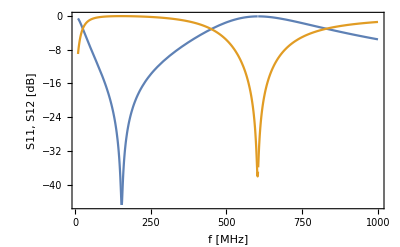

```mathematica
Plot[ Evaluate[20 Log10[Abs[S[[1]]]] //. {C1-> 60 10^(-6),C2->4.2 10^(-6),L2-> 0.0166,Z0->50,R2->0.5,ω->2π ν}],{ν,10,1000},PlotRange->All,Frame->True,FrameLabel->{"f [MHz]", "S11, S12 [dB]"}]
```

### Parallel (Ground-) connected frequency switch

```mathematica
BranchList= {
{{2,3},I ω C1},
{{3,1},I ω C2},
{{3,1}, 1/(I ω L2 + R2)}};
```

```mathematica
PortList= {{2,1},{2,1}}
```

{{2,1},{2,1}}

```mathematica
ZMatrix[3,BranchList,PortList]
```

{{(ⅈ (-1-ⅈ C1 R2 ω-ⅈ C2 R2 ω+C1 L2 ω^2+C2 L2 ω^2))/(C1 ω (-1-ⅈ C2 R2 ω+C2 L2 ω^2)),(ⅈ (-1-ⅈ C1 R2 ω-ⅈ C2 R2 ω+C1 L2 ω^2+C2 L2 ω^2))/(C1 ω (-1-ⅈ C2 R2 ω+C2 L2 ω^2))},{(ⅈ (-1-ⅈ C1 R2 ω-ⅈ C2 R2 ω+C1 L2 ω^2+C2 L2 ω^2))/(C1 ω (-1-ⅈ C2 R2 ω+C2 L2 ω^2)),(ⅈ (-1-ⅈ C1 R2 ω-ⅈ C2 R2 ω+C1 L2 ω^2+C2 L2 ω^2))/(C1 ω (-1-ⅈ C2 R2 ω+C2 L2 ω^2))}}

```mathematica
Timing[S=SMatrix[3,Z0,BranchList,PortList];]
```

{0.029639,Null}

```mathematica
values={C1-> 60 10^(-6),C2->4.2 10^(-6),L2-> 0.0166,Z0->50,R2->0.5,ω->2π ν}
```

{C1→3/50000,C2→4.2×10^-6,L2→0.0166,Z0→50,R2→0.5,ω→2 π ν}

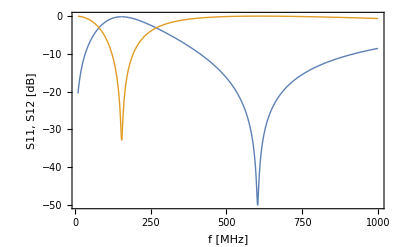

```mathematica
symplot=Plot[ Evaluate[20 Log10[Abs[S[[1]]]] //. values],{ν,10,1000},PlotRange->All,Frame->True,FrameLabel->{"f [MHz]", "S11, S12 [dB]"},PlotStyle->Thin]
```

The above calculations were done symbolically, with explicit frequency dependence of the admittance values carried through. It is also possible to do the same computations numerically, putting the numerical parameters in before the admittance and S matrices are evaluated.

```mathematica
BLN= BranchList /. values
```

{{{2,3},(3 ⅈ π ν)/25000},{{3,1},(0.+0.0000263894 ⅈ) ν},{{3,1},1/(0.5+(0.+0.104301 ⅈ) ν)}}

```mathematica
Timing[S=Table[ SMatrix[3,50.,BLN,PortList],{ν,20,1000,2}];]
```

{0.433592,Null}

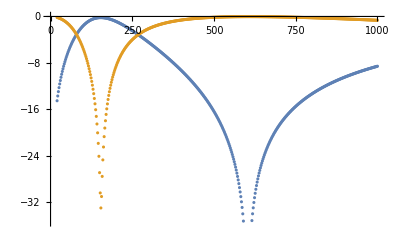

```mathematica
numplot=ListPlot[20Log10[Abs[ {S[[;;,1,1]],S[[;;,1,2]] } ]] ,DataRange->{20,1000}]
```

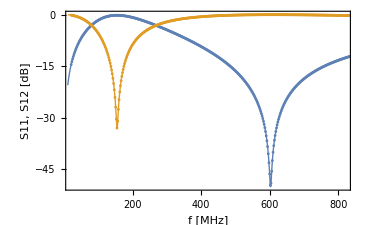

```mathematica
Show[symplot,numplot,PlotRange->{{20,820},All}]
```

## Low-High Switch (cap in parallel with series resonator)

### Series connected

```mathematica
BranchList= {
{{2,4},I ω C1},
{{2,3},I ω C2},
{{3,4}, 1/(I ω L2 + R2)},
{{4,1},1/RPG}};
```

```mathematica
PortList= {{2,1},{4,1}}
```

{{2,1},{4,1}}

```mathematica
ZMatrix[4,BranchList,PortList]
```

{{-(ⅈ-C2 R2 ω-C1 RPG ω-C2 RPG ω-ⅈ C2 L2 ω^2-ⅈ C1 C2 R2 RPG ω^2+C1 C2 L2 RPG ω^3)/(ω (-C1-C2-ⅈ C1 C2 R2 ω+C1 C2 L2 ω^2)),-RPG},{-RPG,-RPG}}

```mathematica
S=Limit[SMatrix[4,Z0,BranchList,PortList] ,RPG->Infinity]
```

{{(ⅈ-C2 ω (R2+ⅈ L2 ω))/(ⅈ-2 C1 Z0 ω+C2 ω (-2 Z0-ⅈ L2 ω+2 C1 L2 Z0 ω^2+R2 (-1-2 ⅈ C1 Z0 ω))),(2 Z0 ω (-C2+C1 (-1+C2 ω (-ⅈ R2+L2 ω))))/(ⅈ-2 C1 Z0 ω+C2 ω (-2 Z0-ⅈ L2 ω+2 C1 L2 Z0 ω^2+R2 (-1-2 ⅈ C1 Z0 ω)))},{(2 Z0 ω (-C2+C1 (-1+C2 ω (-ⅈ R2+L2 ω))))/(ⅈ-2 C1 Z0 ω+C2 ω (-2 Z0-ⅈ L2 ω+2 C1 L2 Z0 ω^2+R2 (-1-2 ⅈ C1 Z0 ω))),(ⅈ-C2 ω (R2+ⅈ L2 ω))/(ⅈ-2 C1 Z0 ω+C2 ω (-2 Z0-ⅈ L2 ω+2 C1 L2 Z0 ω^2+R2 (-1-2 ⅈ C1 Z0 ω)))}}

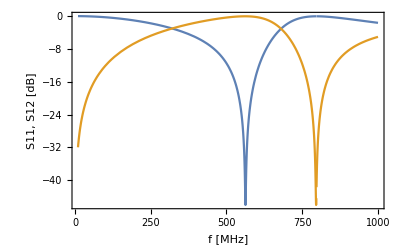

```mathematica
Plot[ Evaluate[20 Log10[Abs[S[[1]]]] //. {C1-> 2 10^(-6),C2->2 10^(-6),L2-> 0.04,Z0->50,R2->0.5,ω->2π ν}],{ν,10,1000},PlotRange->All,Frame->True,FrameLabel->{"f [MHz]", "S11, S12 [dB]"}]
```

### Parallel Connected

```mathematica
BranchList= {
{{2,1},Capacitor[C1]},
{{2,3},Capacitor[C2]},
{{3,1},Inductor[L2,R2]}} /. ComponentRules
```

{{{2,1},ⅈ C1 ω},{{2,3},ⅈ C2 ω},{{3,1},1/(R2+ⅈ L2 ω)}}

```mathematica
PortList= {{2,1},{2,1}}
```

{{2,1},{2,1}}

```mathematica
Timing[S=SMatrix[3,Z0,BranchList,PortList];]
```

{0.057181,Null}

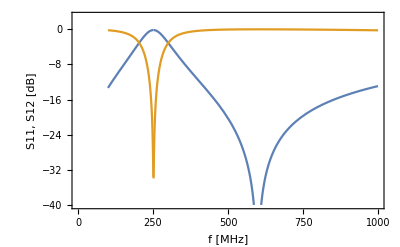

```mathematica
Plot[ Evaluate[20 Log10[Abs[S[[1]]]] //. {C1-> 2.15 10^(-6),C2->10 10^(-6),L2-> 0.04,Z0->50,R2->0.5,ω->2π ν}],{ν,100,1000},PlotRange->{-40,3},Frame->True,FrameLabel->{"f [MHz]", "S11, S12 [dB]"}]
```

The above switch is a passthrough from port 1 to port 2 at 600 MHz (S12=0 dB, S11=–60dB at 600 MHz), and  a block (connection to ground) at 150 MHz. This could for example be used for channel separation in a 1H-13C doubly tuned NMR probe.

```mathematica
Z=ZMatrix[3,BranchList,PortList]
```

{{(ⅈ (-1-ⅈ C2 R2 ω+C2 L2 ω^2))/(ω (-C1-C2-ⅈ C1 C2 R2 ω+C1 C2 L2 ω^2)),(ⅈ (-1-ⅈ C2 R2 ω+C2 L2 ω^2))/(ω (-C1-C2-ⅈ C1 C2 R2 ω+C1 C2 L2 ω^2))},{(ⅈ (-1-ⅈ C2 R2 ω+C2 L2 ω^2))/(ω (-C1-C2-ⅈ C1 C2 R2 ω+C1 C2 L2 ω^2)),(ⅈ (-1-ⅈ C2 R2 ω+C2 L2 ω^2))/(ω (-C1-C2-ⅈ C1 C2 R2 ω+C1 C2 L2 ω^2))}}

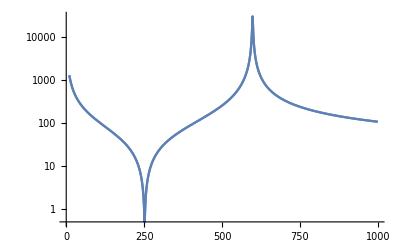

```mathematica
LogPlot[Evaluate[Abs[First@Z]] //. {C1-> 2.15 10^(-6),C2->10 10^(-6),L2-> 0.04,Z0->50,R2->0.5,ω->2π ν},{ν,10,1000},PlotRange->Automatic]
```

## λ/4 Transmission Line Rejection

### Shorted Transmission line

The following shorted transmission line branch is a large impedance at the frequency ω0; therefore, when connected parallel, there is zero reflection and perfect transmission at the target frequency.

```mathematica
BranchList={{{2,1},ShortedTL[ω0,Z0]}} /. ComponentRules
```

{{{2,1},-(ⅈ Cot[(π ω)/(2 ω0)])/Z0}}

```mathematica
PortList={{2,1},{2,1}}
```

{{2,1},{2,1}}

```mathematica
Timing[S=SMatrix[3,Z0,BranchList,PortList];]
```

{0.021962,Null}

```mathematica
S // MatrixForm
```

(-Cot[(π ω)/(2 ω0)]/(2 ⅈ+Cot[(π ω)/(2 ω0)]) | (2 ⅈ)/(2 ⅈ+Cot[(π ω)/(2 ω0)])
(2 Tan[(π ω)/(2 ω0)])/(-ⅈ+2 Tan[(π ω)/(2 ω0)]) | ⅈ/(-ⅈ+2 Tan[(π ω)/(2 ω0)]))

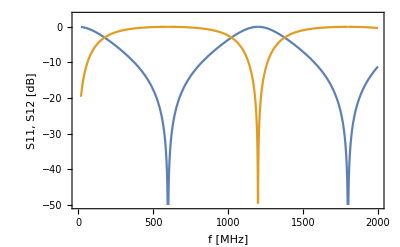

```mathematica
Plot[ Evaluate[20 Log10[Abs[S[[1]]]] //. {ω0->2π 600,Z0->50,R2->0,ω->2π ν}],{ν,20,2000},PlotRange->{-50,3},Frame->True,FrameLabel->{"f [MHz]", "S11, S12 [dB]"}]
```

```mathematica
Z=ZMatrix[3,BranchList,PortList]
```

{{-ⅈ Z0 Tan[(π ω)/(2 ω0)],-ⅈ Z0 Tan[(π ω)/(2 ω0)]},{-ⅈ Z0 Tan[(π ω)/(2 ω0)],-ⅈ Z0 Tan[(π ω)/(2 ω0)]}}

```mathematica
Z//MatrixForm
```

(-ⅈ Z0 Tan[(π ω)/(2 ω0)] | -ⅈ Z0 Tan[(π ω)/(2 ω0)]
-ⅈ Z0 Tan[(π ω)/(2 ω0)] | -ⅈ Z0 Tan[(π ω)/(2 ω0)])

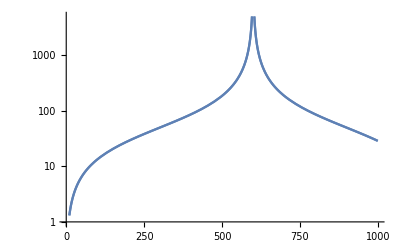

```mathematica
LogPlot[Evaluate[Abs[First@Z]] //. {ω0->2π 600,Z0->50,R2->0.5,ω->2π ν},{ν,10,1000},PlotRange->Automatic]
```

### Open Transmission line

If the transmission line is open at the end, it behaves differently. It now corresponds to a connection to ground at the target frequency; Therefore, the parallel connected open transmission line leads to perfect reflection, and zero transmission, at the target frequency.

```mathematica
BranchList={{{2,1},OpenTL[ω0,Z0]}} /. ComponentRules
```

{{{2,1},-(ⅈ Tan[(π ω)/(2 ω0)])/Z0}}

```mathematica
PortList={{2,1},{2,1}}
```

{{2,1},{2,1}}

```mathematica
Timing[S=SMatrix[3,Z0,BranchList,PortList];]
```

{0.01298,Null}

```mathematica
S //MatrixForm
```

(ⅈ/(-ⅈ+2 Cot[(π ω)/(2 ω0)]) | (2 ⅈ)/(2 ⅈ+Tan[(π ω)/(2 ω0)])
(2 Cot[(π ω)/(2 ω0)])/(-ⅈ+2 Cot[(π ω)/(2 ω0)]) | ⅈ/(-ⅈ+2 Cot[(π ω)/(2 ω0)]))

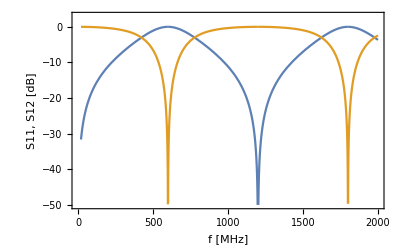

```mathematica
Plot[ Evaluate[20 Log10[Abs[S[[1]]]] //. {ω0->2π 600,Z0->50,R2->0,ω->2π ν}],{ν,20,2000},PlotRange->{-50,3},Frame->True,FrameLabel->{"f [MHz]", "S11, S12 [dB]"}]
```

```mathematica
Z=ZMatrix[3,BranchList,PortList]
```

{{-ⅈ Z0 Cot[(π ω)/(2 ω0)],-ⅈ Z0 Cot[(π ω)/(2 ω0)]},{-ⅈ Z0 Cot[(π ω)/(2 ω0)],-ⅈ Z0 Cot[(π ω)/(2 ω0)]}}

```mathematica
Z//MatrixForm
```

(-ⅈ Z0 Cot[(π ω)/(2 ω0)] | -ⅈ Z0 Cot[(π ω)/(2 ω0)]
-ⅈ Z0 Cot[(π ω)/(2 ω0)] | -ⅈ Z0 Cot[(π ω)/(2 ω0)])